Plots the location of fixed points as a function using the mean-field approach.

## Initialization

```mathematica
Clear["Global`*"]
```

Approximate value of fN

```mathematica
fN1[a0in_]:=Module[{a0=a0in, R,N=121, fa0, G, Acell, L}, 
R = 0.2*a0;
fa0 = Sinh[R]Exp[R-a0]/a0;
G = 2π Exp[R] Sinh[R];
Acell = Sqrt[3]/2 a0^2;
L = Sqrt[ (N-7)Acell/π + (a0/2)^2];
fNest = 6fa0+G/Acell(Exp[-1.5 a0]- Exp[-L]);
fNinf = 6fa0+G/Acell Exp[-1.5 a0]
];
fN1[1]
```

0.940893

```mathematica
params = {Con -> 16,k-> 8,fN-> fNinf, n-> 2};
params2 = {Con -> 8,k-> 15, n-> 2};
```

Values for fN:
N=121, a0 = 0.5 => 
N=121, a0 = 1.5 =>

Updating function

```mathematica
S[x_]:=((Con-1)x+1);
f[xself_,xother_]:=(S[xself]+fN *S[xother])^n/(k^n+(S[xself]+fN *S[xother])^n);
```

Transforming Data

```mathematica
transformData[nsol_, xall_] :=Module[ {t,xvals}, 
xvals=Length/@(xself/.nsol);
t=Table[ ConstantArray[xall[[i]], xvals[[i]]], {i, 1, Length[xvals]}];
Flatten[Transpose/@Transpose[{t,xself/.nsol}], {1,2}]
];
```

## Mean-field approach

```mathematica
Plot3D[ {f[xself, xother] /. params, xself}, {xself,0,1}, {xother,0,1}, PlotRange-> All, BoxRatios->{1, 1, 1},ImageSize->Large, AxesLabel->{"x_self","x_other","f(x_self, x_other)"}, BaseStyle->{FontSize->20}, Mesh-> None, PlotStyle->Directive[Opacity[0.5]], Ticks-> {Automatic,Automatic, Automatic}]
```

-Graphics3D-

### Numerically find fixed points

```mathematica
dX = 0.001;
thisa0 =1.5;
sol = Table[
NSolve[ {((f[xself, xother ] - xself) /. params2 /. {fN-> fN1[thisa0]}) == 0,0≤xself≤ 1}, xself] ,
{xother,0,1, dX}];
plotdata = transformData[sol,Range[0,1,dX]];
```

Plot data

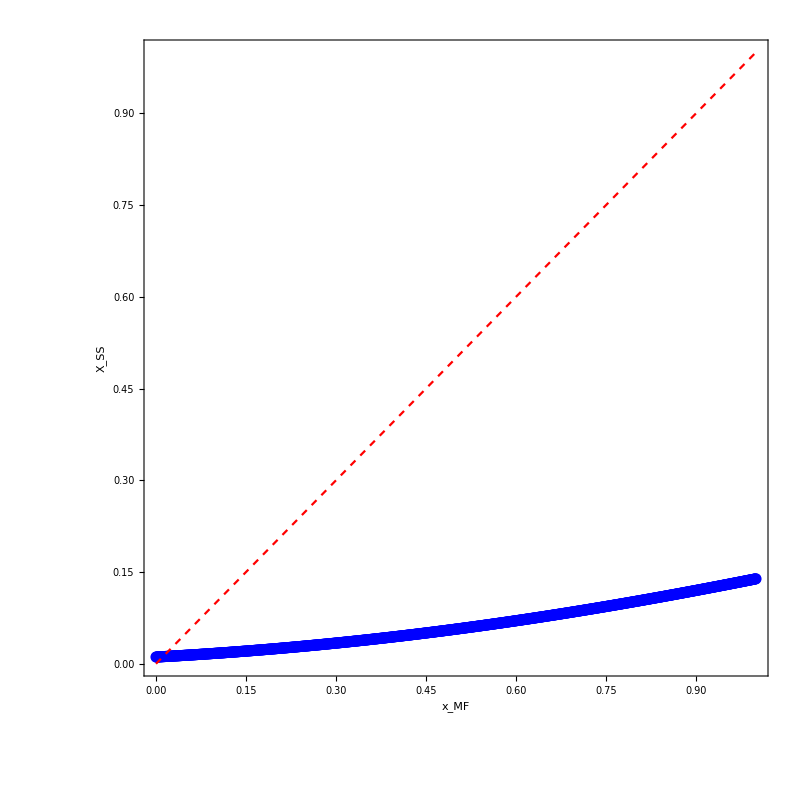

```mathematica
fstyle = Style[#,16] & ;
l1 = Placed[SwatchLegend[fstyle/@{"n=2"}, LegendMarkerSize->5],Above]; 
p1=ListPlot[plotdata, PlotStyle-> {Blue, PointSize-> 0.01}];
p2 = Plot[x, {x,0,1}, PlotStyle-> {Red, Dashed, Thickness[0.002]}];
fig2=Show[p1,p2,ImageSize-> 800,BaseStyle-> {FontSize-> 50}, Frame-> True, FrameLabel-> {"x_MF", "X_SS"}, PlotRange-> All, AxesOrigin-> {0,0}, AspectRatio->1]
```

```mathematica
(*SetDirectory["H:\\My Documents\\Thesis\\Single gene finite Hill\\2_finite_Hill_nonuniform\\fig_mean_field"];
Export["finite_Hill_mean_field_fixed_points_N121_K8_Con16_n2_a0_7p0.pdf",fig2] 
*)
```

finite_Hill_mean_field_fixed_points_N121_K8_Con16_n2_a0_7p0.pdf

### Variability upper bound

Derive an upper bound for variability of ON and OFF cells.
E.g. take Δx_self=x_self(x_other=1)-x_self(x_other=0) for ON.

```mathematica
{xself/.Flatten[nsol[[-1]]]}[[1]]  - {xself/.Flatten[nsol[[1]]]}[[1]]
```

Part::partd: Part specification nsol⟦-1⟧ is longer than depth of object.

ReplaceAll::reps: {nsol⟦-1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification nsol⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {nsol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(xself/.nsol⟦-1⟧)-(xself/.nsol⟦1⟧)

ON cells

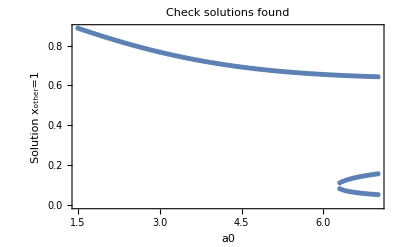

```mathematica
a0lims = {1.5,7.0,0.05}; (*start, end, di*)
a0data = Range[a0lims[[1]], a0lims[[2]], a0lims[[3]]];
solx0 = Table[
NSolve[ {((f[xself, 0] - xself) /. params2 /. {fN-> fN1[a0]}) == 0,0≤xself≤ 1}, xself] ,
{a0, a0lims[[1]],a0lims[[2]],a0lims[[3]]}];
solx1 = Table[
NSolve[ {((f[xself, 1] - xself) /. params2 /. {fN-> fN1[a0]}) == 0,0≤xself≤ 1}, xself] ,
{a0, a0lims[[1]],a0lims[[2]],a0lims[[3]]}];

plotDatax1 =transformData[solx1, a0data];
ListPlot[plotDatax1, PlotLabel->"Check solutions found", Frame->True, FrameLabel->{"a0", "Solution x_other=1"}]
```

OFF cells

```mathematica
x2Vals = ConstantArray[1,Length[a0data]]; (*Set to 1 very important, default if l==1 not found*)
xotherVals = Range[0,1,0.001];
Table[
a0=a0data[[a0ind]];
For[i=1, i< Length@xotherVals, i++,
l = Length@Flatten@NSolve[ {((f[xself, xotherVals[[i]]] - xself) /. params2 /. {fN-> fN1[a0]}) == 0,0≤xself≤ 1}, xself];
If[l==1,
x2Vals[[a0ind]]=xotherVals[[i-1]];
(* Print[x2Vals[[a0ind]]]; *)
Break[];
];
],
{a0ind, 1, Length[a0data]}];
solx2 =Table[
NSolve[ {((f[ xself, x2Vals[[i]] ] - xself) /. params2 /. {fN-> fN1[a0data[[i]]]}) == 0,0≤xself≤ 1}, xself] ,
{i,1,Length[x2Vals]}];
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

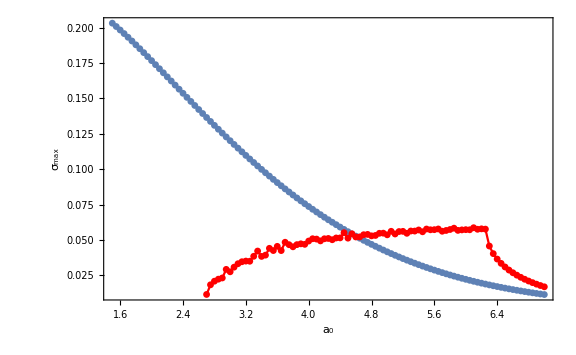

```mathematica
plotDataON = Transpose[{a0data,Max/@(xself/.solx1)-Max/@(xself/.solx0)}];
plotDataOFF = Transpose[{a0data,Min/@(xself/.solx2)-Min/@(xself/.solx0)}];
plot1=ListPlot[plotDataON, Joined-> True, PlotMarkers->{Automatic,7}]; (*, Frame->True, FrameLabel->{"a_0", "σ_max"},ImageSize-> Large,BaseStyle-> {FontSize-> 20}]*)
plot2=ListPlot[plotDataOFF, PlotStyle-> {Red}, Joined-> True, PlotMarkers->{Automatic,7}];
fig3 = Show[plot1,plot2,Frame->True, FrameLabel->{"a_0", "σ_max"},ImageSize-> Large,BaseStyle-> {FontSize-> 32}, PlotRange-> All]
```

Export data (for integration with MATLAB)

```mathematica
(*
SetDirectory[NotebookDirectory[]];
Export["max_variance_cells_vs_a0_ON.XLS",plotDataON]
Export["max_variance_cells_vs_a0_OFF.XLS",plotDataOFF]
*)
```

Export figure

```mathematica
SetDirectory["H:\\My Documents\\Thesis\\Single gene finite Hill\\2_finite_Hill_nonuniform\\fig_transition_spread"];
Export["Spread_avg_a0_1p5to7p0_N121_K8_Con16_hill_2p0_binaryrand_blueON_redOFF.pdf",fig3]
```

Spread_avg_a0_1p5to7p0_N121_K8_Con16_hill_2p0_binaryrand_blueON_redOFF.pdf

## All fixed points vs a_0

### Numerically find fixed points

```mathematica
dX = 0.001;
thisa0 =5;
thisxsol = x/.NSolve[{f[x, x] - x == 0/. params2 /. {fN-> fN1[thisa0]}},x]
```

{0.664259,0.160797,0.0416104}

```mathematica
xsol=Table[x/.NSolve[{f[x, x] - x == 0/. params2 /. {fN-> fN1[a0]}},x∈ Reals], {a0,3.0,6.0,0.01}];
a0list = Range[3,6,0.01];
a0list2 = Table[ConstantArray[a0list[[i]],  xsol[[i]]//Length], {i,1, Length[xsol]}];
```

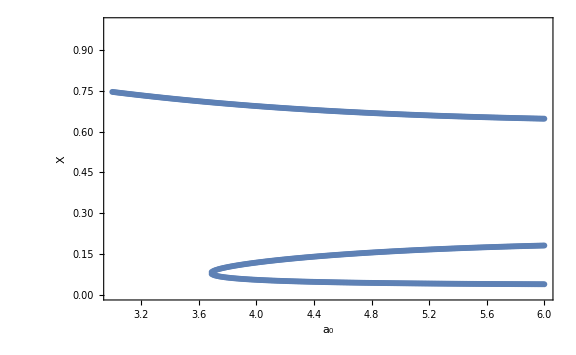

```mathematica
p1=ListPlot[Flatten[Transpose/@Transpose[{a0list2, xsol}], 1], ImageSize-> Large,BaseStyle-> {FontSize-> 20},Frame->True, FrameLabel-> {"a_0", "X"}, PlotRange-> {Automatic, {0,1}}]
```